```mathematica
g=9.8; (*grav. constant*)
vt=25
V=30
th=50 (Pi/180)
ode1={x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]}
ode2 ={y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2])}
sol=NDSolve[{ode1,ode2, x[0]==0,x'[0]==V Cos[th], y[0]==2, y'[0]==V Sin[th]},{x,y},{t,0,200}]
```

25

30

(5 π)/18

{x''[t]==-0.01568 x'[t] √(x'[t]^2+y'[t]^2)}

{y''[t]==-9.8 (1+1/625 y'[t] √(x'[t]^2+y'[t]^2))}

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

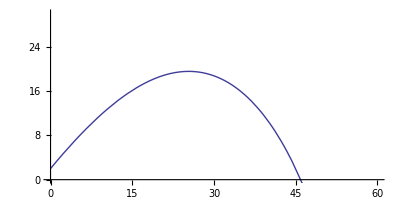

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol], {t,0,200},PlotRange-> {{0,60},{0,30}}]
```

```mathematica
Manipulate[
g=9.8;
Module[
{result = NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2],y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]), x[0]==x0,x'[0]==V Cos[th], y[0]==y0, y'[0]==V Sin[th]},{x,y},{t,0,tf}]},
ParametricPlot[{{x0+V Cos[th] t, y0+V Sin[th] t-(1/2)g t^2},{Evaluate[{x[t],y[t]}/.result]}},{t,0,tf},PlotStyle-> {{Blue},{Red}},PlotRange-> {{0,3000},{-10,500}},AxesLabel->{"x (m)","y (m)"},PlotRange->{{-1,100},{-1,200}},ImageSize->{500,300}]],
{{vt,10,"terminal velocity (m/s)"},.1,200,Appearance->"Labeled"},
{{V,10,"velocity (m/s)"},.1,500,Appearance->"Labeled"},
{{th,Pi/6,"initial angle (rad)"},0,Pi/2,Appearance->"Labeled"},
{{x0, 0, "initial x position (m)"}, 0, 20, Appearance-> "Labeled"},
{{y0, 0, "initial hight (m)"}, 0, 20, Appearance-> "Labeled"},
{{tf, 10, "time (s)"}, 0, 200, Appearance-> "Labeled"}]
```